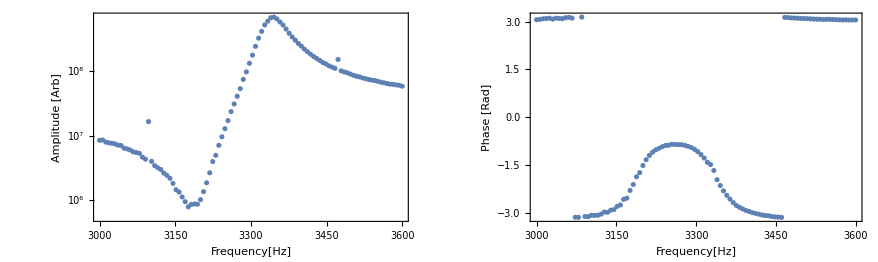

```mathematica
THEDATAFILENAME="VNA_output.csv";

SetDirectory[NotebookDirectory[]];
thedat=Import[THEDATAFILENAME];
fulldat=Table[{N[thedat[[jj,1]]],N[ToExpression[StringSplit[StringReplace[thedat[[jj,2]],{"["->"","]"->"","L"->""}],","]]]},{jj,1,Length[thedat]}];
GraphicsGrid[{{ListLogPlot[Transpose[{fulldat[[;;,1]],Abs[fulldat[[;;,2,1]]+I fulldat[[;;,2,2]]]^2}],Frame->True,FrameLabel->{"Frequency[Hz]","Amplitude [Arb]"}],
ListPlot[Transpose[{fulldat[[;;,1]],Arg[fulldat[[;;,2,1]]+I fulldat[[;;,2,2]]]}],PlotRange->All,Frame->True,FrameLabel->{"Frequency[Hz]","Phase [Rad]"}]}}]
```